```mathematica
J=1
A =1
 gamma= 1
Timing[Jkrj=Table[u/.FindRoot[A×x^-3×ⅇ^(-J×x)×(ⅇ^-u+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-u×l)×∑_(n=1)^l ⅇ^(-vibration x Cos[(n π)/(2 l)]))-1,{u,-3},MaxIterations->10000],{vibration,{0.001,1,100,1000,100000}},{x,0.01,20,0.1}]]
```

1

1

1

General::munfl: 176.999/(203929827411891162469297604499861487470751456486742359827810683408539939«168»875200268932124981878786621440000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (177.999 89)/(314072098062416037868220893164838362402594800436966192929957494404364935«172»196699124005923162587377172480000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (178.999 32041)/(196791295203948641007469847239224421114217850057794277166052766843886981«177»773711963133521399878873251840000000000000000000000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{15091.4,{{13.8055,6.52362,4.55803,3.4693,2.80038,2.35647,2.03657,1.78976,1.58951,1.42102,1.27542,1.14705,1.03209,0.927881,0.832471,0.744407,0.662572,0.586087,0.514253,0.4465,0.382359,0.32144,0.263414,0.208001,0.154962,0.104089,0.0552015,0.0081409,-0.0372321,-0.0810411,-0.123396,-0.164396,-0.204129,-0.242675,-0.280106,-0.316488,-0.351881,-0.386339,-0.419912,-0.452647,-0.484585,-0.515767,-0.546228,-0.576001,-0.605119,-0.633609,-0.6615,-0.688816,-0.715581,-0.741818,-0.767547,-0.792788,-0.817559,-0.841877,-0.86576,-0.889222,-0.912278,-0.934942,-0.957227,-0.979146,-1.00071,-1.02193,-1.04282,-1.06339,-1.08364,-1.10359,-1.12325,-1.14262,-1.16171,-1.18053,-1.19909,-1.21739,-1.23545,-1.25326,-1.27084,-1.28819,-1.30531,-1.32221,-1.3389,-1.35539,-1.37167,-1.38775,-1.40364,-1.41934,-1.43485,-1.45018,-1.46534,-1.48032,-1.49514,-1.50979,-1.52428,-1.53861,-1.55278,-1.5668,-1.58068,-1.5944,-1.60799,-1.62143,-1.63474,-1.64791,-1.66095,-1.67386,-1.68665,-1.6993,-1.71184,-1.72425,-1.73655,-1.74873,-1.7608,-1.77275,-1.7846,-1.79634,-1.80797,-1.81949,-1.83092,-1.84224,-1.85346,-1.86459,-1.87562,-1.88655,-1.89739,-1.90814,-1.9188,-1.92938,-1.93986,-1.95026,-1.96057,-1.9708,-1.98095,-1.99102,-2.00101,-2.01092,-2.02075,-2.0305,-2.04019,-2.04979,-2.05933,-2.06879,-2.07818,-2.0875,-2.09675,-2.10594,-2.11505,-2.12411,-2.13309,-2.14201,-2.15087,-2.15967,-2.1684,-2.17707,-2.18568,-2.19424,-2.20273,-2.21117,-2.21954,-2.22787,-2.23613,-2.24434,-2.2525,-2.26061,-2.26866,-2.27665,-2.2846,-2.29249,-2.30034,-2.30813,-2.31588,-2.32357,-2.33122,-2.33882,-2.34638,-2.35388,-2.36134,-2.36876,-2.37613,-2.38346,-2.39074,-2.39798,-2.40517,-2.41232,-2.41943,-2.4265,-2.43353,-2.44052,-2.44747,-2.45437,-2.46124,-2.46807,-2.47486,-2.48162,-2.48833,-2.49501,-2.50165,-2.50825,-2.51482,-2.52135,-2.52785,-2.53431,-2.54073,-2.54713},{13.8055,6.52318,4.55266,3.44985,2.76172,2.29944,1.96365,1.70315,1.4909,1.31171,1.15646,1.01929,0.896276,0.784649,0.682396,0.588005,0.500311,0.418399,0.341534,0.269117,0.200656,0.135735,0.0740047,0.0151668,-0.0410368,-0.0948297,-0.146408,-0.195943,-0.243589,-0.289481,-0.333741,-0.376478,-0.41779,-0.457768,-0.496493,-0.534037,-0.57047,-0.605854,-0.640244,-0.673695,-0.706255,-0.737969,-0.768878,-0.799021,-0.828436,-0.857154,-0.885208,-0.912627,-0.939438,-0.965668,-0.991341,-1.01648,-1.0411,-1.06523,-1.08889,-1.11209,-1.13486,-1.1572,-1.17913,-1.20067,-1.22183,-1.24262,-1.26306,-1.28316,-1.30292,-1.32237,-1.3415,-1.36034,-1.37888,-1.39714,-1.41512,-1.43284,-1.4503,-1.4675,-1.48447,-1.50119,-1.51768,-1.53395,-1.55,-1.56584,-1.58147,-1.5969,-1.61213,-1.62716,-1.64201,-1.65668,-1.67117,-1.68548,-1.69962,-1.7136,-1.72741,-1.74106,-1.75456,-1.76791,-1.7811,-1.79416,-1.80707,-1.81984,-1.83247,-1.84497,-1.85734,-1.86958,-1.88169,-1.89368,-1.90555,-1.9173,-1.92894,-1.94046,-1.95187,-1.96317,-1.97436,-1.98545,-1.99643,-2.00731,-2.01809,-2.02877,-2.03935,-2.04984,-2.06024,-2.07054,-2.08076,-2.09088,-2.10092,-2.11087,-2.12074,-2.13053,-2.14023,-2.14985,-2.1594,-2.16886,-2.17825,-2.18757,-2.19681,-2.20597,-2.21507,-2.22409,-2.23305,-2.24193,-2.25075,-2.2595,-2.26818,-2.2768,-2.28536,-2.29385,-2.30228,-2.31065,-2.31895,-2.3272,-2.33539,-2.34352,-2.3516,-2.35961,-2.36758,-2.37548,-2.38334,-2.39113,-2.39888,-2.40657,-2.41422,-2.42181,-2.42935,-2.43684,-2.44429,-2.45168,-2.45903,-2.46633,-2.47358,-2.48079,-2.48795,-2.49507,-2.50214,-2.50917,-2.51615,-2.52309,-2.52999,-2.53685,-2.54367,-2.55045,-2.55718,-2.56388,-2.57053,-2.57715,-2.58373,-2.59027,-2.59677,-2.60324,-2.60967,-2.61606,-2.62242,-2.62874,-2.63502,-2.64127,-2.64749,-2.65367,-2.65981,-2.66593,-2.67201,-2.67806,-2.68407,-2.69005},{13.8055,6.51776,4.5168,3.35433,2.60442,2.10129,1.74506,1.47688,1.26406,1.08815,0.938246,0.807526,0.691494,0.587056,0.492004,0.404705,0.323925,0.248705,0.178288,0.112063,0.0495311,-0.00971911,-0.0660334,-0.119704,-0.17098,-0.220078,-0.267182,-0.312456,-0.356044,-0.39807,-0.438649,-0.47788,-0.515853,-0.55265,-0.588343,-0.622998,-0.656677,-0.689433,-0.721319,-0.75238,-0.782658,-0.812193,-0.841021,-0.869177,-0.89669,-0.923591,-0.949907,-0.975662,-1.00088,-1.02558,-1.04979,-1.07353,-1.09681,-1.11965,-1.14207,-1.16408,-1.1857,-1.20694,-1.22781,-1.24833,-1.26851,-1.28836,-1.30789,-1.32711,-1.34603,-1.36466,-1.38301,-1.40108,-1.41888,-1.43643,-1.45373,-1.47078,-1.48759,-1.50418,-1.52054,-1.53668,-1.5526,-1.56832,-1.58384,-1.59916,-1.61428,-1.62922,-1.64397,-1.65855,-1.67295,-1.68718,-1.70124,-1.71514,-1.72888,-1.74246,-1.7559,-1.76918,-1.78231,-1.79531,-1.80816,-1.82087,-1.83345,-1.8459,-1.85822,-1.87042,-1.88249,-1.89443,-1.90626,-1.91798,-1.92957,-1.94106,-1.95243,-1.9637,-1.97486,-1.98591,-1.99686,-2.00772,-2.01847,-2.02912,-2.03968,-2.05015,-2.06052,-2.0708,-2.08099,-2.0911,-2.10112,-2.11105,-2.1209,-2.13067,-2.14035,-2.14996,-2.15949,-2.16894,-2.17831,-2.18761,-2.19684,-2.20599,-2.21507,-2.22409,-2.23303,-2.2419,-2.25071,-2.25945,-2.26812,-2.27673,-2.28528,-2.29376,-2.30218,-2.31054,-2.31884,-2.32708,-2.33526,-2.34339,-2.35146,-2.35947,-2.36742,-2.37532,-2.38317,-2.39097,-2.39871,-2.4064,-2.41403,-2.42162,-2.42916,-2.43665,-2.44409,-2.45148,-2.45882,-2.46612,-2.47337,-2.48057,-2.48773,-2.49484,-2.50191,-2.50894,-2.51592,-2.52286,-2.52976,-2.53662,-2.54343,-2.55021,-2.55694,-2.56364,-2.57029,-2.57691,-2.58349,-2.59002,-2.59653,-2.60299,-2.60942,-2.61581,-2.62217,-2.62849,-2.63477,-2.64102,-2.64724,-2.65342,-2.65956,-2.66568,-2.67176,-2.67781,-2.68382,-2.6898,-2.69576,-2.70168},{13.8055,6.51775,4.5168,3.35433,2.60442,2.10129,1.74506,1.47688,1.26406,1.08815,0.938246,0.807526,0.691494,0.587056,0.492004,0.404705,0.323925,0.248705,0.178288,0.112063,0.0495311,-0.00971911,-0.0660334,-0.119704,-0.17098,-0.220078,-0.267182,-0.312456,-0.356044,-0.39807,-0.438649,-0.47788,-0.515853,-0.55265,-0.588343,-0.622998,-0.656677,-0.689433,-0.721319,-0.75238,-0.782658,-0.812193,-0.841021,-0.869177,-0.89669,-0.923591,-0.949907,-0.975662,-1.00088,-1.02558,-1.04979,-1.07353,-1.09681,-1.11965,-1.14207,-1.16408,-1.1857,-1.20694,-1.22781,-1.24833,-1.26851,-1.28836,-1.30789,-1.32711,-1.34603,-1.36466,-1.38301,-1.40108,-1.41888,-1.43643,-1.45373,-1.47078,-1.48759,-1.50418,-1.52054,-1.53668,-1.5526,-1.56832,-1.58384,-1.59916,-1.61428,-1.62922,-1.64397,-1.65855,-1.67295,-1.68718,-1.70124,-1.71514,-1.72888,-1.74246,-1.7559,-1.76918,-1.78231,-1.79531,-1.80816,-1.82087,-1.83345,-1.8459,-1.85822,-1.87042,-1.88249,-1.89443,-1.90626,-1.91798,-1.92957,-1.94106,-1.95243,-1.9637,-1.97486,-1.98591,-1.99686,-2.00772,-2.01847,-2.02912,-2.03968,-2.05015,-2.06052,-2.0708,-2.08099,-2.0911,-2.10112,-2.11105,-2.1209,-2.13067,-2.14035,-2.14996,-2.15949,-2.16894,-2.17831,-2.18761,-2.19684,-2.20599,-2.21507,-2.22409,-2.23303,-2.2419,-2.25071,-2.25945,-2.26812,-2.27673,-2.28528,-2.29376,-2.30218,-2.31054,-2.31884,-2.32708,-2.33526,-2.34339,-2.35146,-2.35947,-2.36742,-2.37532,-2.38317,-2.39097,-2.39871,-2.4064,-2.41403,-2.42162,-2.42916,-2.43665,-2.44409,-2.45148,-2.45882,-2.46612,-2.47337,-2.48057,-2.48773,-2.49484,-2.50191,-2.50894,-2.51592,-2.52286,-2.52976,-2.53662,-2.54343,-2.55021,-2.55694,-2.56364,-2.57029,-2.57691,-2.58349,-2.59002,-2.59653,-2.60299,-2.60942,-2.61581,-2.62217,-2.62849,-2.63477,-2.64102,-2.64724,-2.65342,-2.65956,-2.66568,-2.67176,-2.67781,-2.68382,-2.6898,-2.69576,-2.70168},{13.8055,6.51775,4.5168,3.35433,2.60442,2.10129,1.74506,1.47688,1.26406,1.08815,0.938246,0.807526,0.691494,0.587056,0.492004,0.404705,0.323925,0.248705,0.178288,0.112063,0.0495311,-0.00971911,-0.0660334,-0.119704,-0.17098,-0.220078,-0.267182,-0.312456,-0.356044,-0.39807,-0.438649,-0.47788,-0.515853,-0.55265,-0.588343,-0.622998,-0.656677,-0.689433,-0.721319,-0.75238,-0.782658,-0.812193,-0.841021,-0.869177,-0.89669,-0.923591,-0.949907,-0.975662,-1.00088,-1.02558,-1.04979,-1.07353,-1.09681,-1.11965,-1.14207,-1.16408,-1.1857,-1.20694,-1.22781,-1.24833,-1.26851,-1.28836,-1.30789,-1.32711,-1.34603,-1.36466,-1.38301,-1.40108,-1.41888,-1.43643,-1.45373,-1.47078,-1.48759,-1.50418,-1.52054,-1.53668,-1.5526,-1.56832,-1.58384,-1.59916,-1.61428,-1.62922,-1.64397,-1.65855,-1.67295,-1.68718,-1.70124,-1.71514,-1.72888,-1.74246,-1.7559,-1.76918,-1.78231,-1.79531,-1.80816,-1.82087,-1.83345,-1.8459,-1.85822,-1.87042,-1.88249,-1.89443,-1.90626,-1.91798,-1.92957,-1.94106,-1.95243,-1.9637,-1.97486,-1.98591,-1.99686,-2.00772,-2.01847,-2.02912,-2.03968,-2.05015,-2.06052,-2.0708,-2.08099,-2.0911,-2.10112,-2.11105,-2.1209,-2.13067,-2.14035,-2.14996,-2.15949,-2.16894,-2.17831,-2.18761,-2.19684,-2.20599,-2.21507,-2.22409,-2.23303,-2.2419,-2.25071,-2.25945,-2.26812,-2.27673,-2.28528,-2.29376,-2.30218,-2.31054,-2.31884,-2.32708,-2.33526,-2.34339,-2.35146,-2.35947,-2.36742,-2.37532,-2.38317,-2.39097,-2.39871,-2.4064,-2.41403,-2.42162,-2.42916,-2.43665,-2.44409,-2.45148,-2.45882,-2.46612,-2.47337,-2.48057,-2.48773,-2.49484,-2.50191,-2.50894,-2.51592,-2.52286,-2.52976,-2.53662,-2.54343,-2.55021,-2.55694,-2.56364,-2.57029,-2.57691,-2.58349,-2.59002,-2.59653,-2.60299,-2.60942,-2.61581,-2.62217,-2.62849,-2.63477,-2.64102,-2.64724,-2.65342,-2.65956,-2.66568,-2.67176,-2.67781,-2.68382,-2.6898,-2.69576,-2.70168}}}

```mathematica
J05 = Jkrj[[1]]
J1 = Jkrj[[2]]
J105 = Jkrj[[3]]
J2 = Jkrj[[4]]
J205=Jkrj[[5]]
```

{13.8055,6.52362,4.55803,3.4693,2.80038,2.35647,2.03657,1.78976,1.58951,1.42102,1.27542,1.14705,1.03209,0.927881,0.832471,0.744407,0.662572,0.586087,0.514253,0.4465,0.382359,0.32144,0.263414,0.208001,0.154962,0.104089,0.0552015,0.0081409,-0.0372321,-0.0810411,-0.123396,-0.164396,-0.204129,-0.242675,-0.280106,-0.316488,-0.351881,-0.386339,-0.419912,-0.452647,-0.484585,-0.515767,-0.546228,-0.576001,-0.605119,-0.633609,-0.6615,-0.688816,-0.715581,-0.741818,-0.767547,-0.792788,-0.817559,-0.841877,-0.86576,-0.889222,-0.912278,-0.934942,-0.957227,-0.979146,-1.00071,-1.02193,-1.04282,-1.06339,-1.08364,-1.10359,-1.12325,-1.14262,-1.16171,-1.18053,-1.19909,-1.21739,-1.23545,-1.25326,-1.27084,-1.28819,-1.30531,-1.32221,-1.3389,-1.35539,-1.37167,-1.38775,-1.40364,-1.41934,-1.43485,-1.45018,-1.46534,-1.48032,-1.49514,-1.50979,-1.52428,-1.53861,-1.55278,-1.5668,-1.58068,-1.5944,-1.60799,-1.62143,-1.63474,-1.64791,-1.66095,-1.67386,-1.68665,-1.6993,-1.71184,-1.72425,-1.73655,-1.74873,-1.7608,-1.77275,-1.7846,-1.79634,-1.80797,-1.81949,-1.83092,-1.84224,-1.85346,-1.86459,-1.87562,-1.88655,-1.89739,-1.90814,-1.9188,-1.92938,-1.93986,-1.95026,-1.96057,-1.9708,-1.98095,-1.99102,-2.00101,-2.01092,-2.02075,-2.0305,-2.04019,-2.04979,-2.05933,-2.06879,-2.07818,-2.0875,-2.09675,-2.10594,-2.11505,-2.12411,-2.13309,-2.14201,-2.15087,-2.15967,-2.1684,-2.17707,-2.18568,-2.19424,-2.20273,-2.21117,-2.21954,-2.22787,-2.23613,-2.24434,-2.2525,-2.26061,-2.26866,-2.27665,-2.2846,-2.29249,-2.30034,-2.30813,-2.31588,-2.32357,-2.33122,-2.33882,-2.34638,-2.35388,-2.36134,-2.36876,-2.37613,-2.38346,-2.39074,-2.39798,-2.40517,-2.41232,-2.41943,-2.4265,-2.43353,-2.44052,-2.44747,-2.45437,-2.46124,-2.46807,-2.47486,-2.48162,-2.48833,-2.49501,-2.50165,-2.50825,-2.51482,-2.52135,-2.52785,-2.53431,-2.54073,-2.54713}

{13.8055,6.52318,4.55266,3.44985,2.76172,2.29944,1.96365,1.70315,1.4909,1.31171,1.15646,1.01929,0.896276,0.784649,0.682396,0.588005,0.500311,0.418399,0.341534,0.269117,0.200656,0.135735,0.0740047,0.0151668,-0.0410368,-0.0948297,-0.146408,-0.195943,-0.243589,-0.289481,-0.333741,-0.376478,-0.41779,-0.457768,-0.496493,-0.534037,-0.57047,-0.605854,-0.640244,-0.673695,-0.706255,-0.737969,-0.768878,-0.799021,-0.828436,-0.857154,-0.885208,-0.912627,-0.939438,-0.965668,-0.991341,-1.01648,-1.0411,-1.06523,-1.08889,-1.11209,-1.13486,-1.1572,-1.17913,-1.20067,-1.22183,-1.24262,-1.26306,-1.28316,-1.30292,-1.32237,-1.3415,-1.36034,-1.37888,-1.39714,-1.41512,-1.43284,-1.4503,-1.4675,-1.48447,-1.50119,-1.51768,-1.53395,-1.55,-1.56584,-1.58147,-1.5969,-1.61213,-1.62716,-1.64201,-1.65668,-1.67117,-1.68548,-1.69962,-1.7136,-1.72741,-1.74106,-1.75456,-1.76791,-1.7811,-1.79416,-1.80707,-1.81984,-1.83247,-1.84497,-1.85734,-1.86958,-1.88169,-1.89368,-1.90555,-1.9173,-1.92894,-1.94046,-1.95187,-1.96317,-1.97436,-1.98545,-1.99643,-2.00731,-2.01809,-2.02877,-2.03935,-2.04984,-2.06024,-2.07054,-2.08076,-2.09088,-2.10092,-2.11087,-2.12074,-2.13053,-2.14023,-2.14985,-2.1594,-2.16886,-2.17825,-2.18757,-2.19681,-2.20597,-2.21507,-2.22409,-2.23305,-2.24193,-2.25075,-2.2595,-2.26818,-2.2768,-2.28536,-2.29385,-2.30228,-2.31065,-2.31895,-2.3272,-2.33539,-2.34352,-2.3516,-2.35961,-2.36758,-2.37548,-2.38334,-2.39113,-2.39888,-2.40657,-2.41422,-2.42181,-2.42935,-2.43684,-2.44429,-2.45168,-2.45903,-2.46633,-2.47358,-2.48079,-2.48795,-2.49507,-2.50214,-2.50917,-2.51615,-2.52309,-2.52999,-2.53685,-2.54367,-2.55045,-2.55718,-2.56388,-2.57053,-2.57715,-2.58373,-2.59027,-2.59677,-2.60324,-2.60967,-2.61606,-2.62242,-2.62874,-2.63502,-2.64127,-2.64749,-2.65367,-2.65981,-2.66593,-2.67201,-2.67806,-2.68407,-2.69005}

{13.8055,6.51776,4.5168,3.35433,2.60442,2.10129,1.74506,1.47688,1.26406,1.08815,0.938246,0.807526,0.691494,0.587056,0.492004,0.404705,0.323925,0.248705,0.178288,0.112063,0.0495311,-0.00971911,-0.0660334,-0.119704,-0.17098,-0.220078,-0.267182,-0.312456,-0.356044,-0.39807,-0.438649,-0.47788,-0.515853,-0.55265,-0.588343,-0.622998,-0.656677,-0.689433,-0.721319,-0.75238,-0.782658,-0.812193,-0.841021,-0.869177,-0.89669,-0.923591,-0.949907,-0.975662,-1.00088,-1.02558,-1.04979,-1.07353,-1.09681,-1.11965,-1.14207,-1.16408,-1.1857,-1.20694,-1.22781,-1.24833,-1.26851,-1.28836,-1.30789,-1.32711,-1.34603,-1.36466,-1.38301,-1.40108,-1.41888,-1.43643,-1.45373,-1.47078,-1.48759,-1.50418,-1.52054,-1.53668,-1.5526,-1.56832,-1.58384,-1.59916,-1.61428,-1.62922,-1.64397,-1.65855,-1.67295,-1.68718,-1.70124,-1.71514,-1.72888,-1.74246,-1.7559,-1.76918,-1.78231,-1.79531,-1.80816,-1.82087,-1.83345,-1.8459,-1.85822,-1.87042,-1.88249,-1.89443,-1.90626,-1.91798,-1.92957,-1.94106,-1.95243,-1.9637,-1.97486,-1.98591,-1.99686,-2.00772,-2.01847,-2.02912,-2.03968,-2.05015,-2.06052,-2.0708,-2.08099,-2.0911,-2.10112,-2.11105,-2.1209,-2.13067,-2.14035,-2.14996,-2.15949,-2.16894,-2.17831,-2.18761,-2.19684,-2.20599,-2.21507,-2.22409,-2.23303,-2.2419,-2.25071,-2.25945,-2.26812,-2.27673,-2.28528,-2.29376,-2.30218,-2.31054,-2.31884,-2.32708,-2.33526,-2.34339,-2.35146,-2.35947,-2.36742,-2.37532,-2.38317,-2.39097,-2.39871,-2.4064,-2.41403,-2.42162,-2.42916,-2.43665,-2.44409,-2.45148,-2.45882,-2.46612,-2.47337,-2.48057,-2.48773,-2.49484,-2.50191,-2.50894,-2.51592,-2.52286,-2.52976,-2.53662,-2.54343,-2.55021,-2.55694,-2.56364,-2.57029,-2.57691,-2.58349,-2.59002,-2.59653,-2.60299,-2.60942,-2.61581,-2.62217,-2.62849,-2.63477,-2.64102,-2.64724,-2.65342,-2.65956,-2.66568,-2.67176,-2.67781,-2.68382,-2.6898,-2.69576,-2.70168}

{13.8055,6.51775,4.5168,3.35433,2.60442,2.10129,1.74506,1.47688,1.26406,1.08815,0.938246,0.807526,0.691494,0.587056,0.492004,0.404705,0.323925,0.248705,0.178288,0.112063,0.0495311,-0.00971911,-0.0660334,-0.119704,-0.17098,-0.220078,-0.267182,-0.312456,-0.356044,-0.39807,-0.438649,-0.47788,-0.515853,-0.55265,-0.588343,-0.622998,-0.656677,-0.689433,-0.721319,-0.75238,-0.782658,-0.812193,-0.841021,-0.869177,-0.89669,-0.923591,-0.949907,-0.975662,-1.00088,-1.02558,-1.04979,-1.07353,-1.09681,-1.11965,-1.14207,-1.16408,-1.1857,-1.20694,-1.22781,-1.24833,-1.26851,-1.28836,-1.30789,-1.32711,-1.34603,-1.36466,-1.38301,-1.40108,-1.41888,-1.43643,-1.45373,-1.47078,-1.48759,-1.50418,-1.52054,-1.53668,-1.5526,-1.56832,-1.58384,-1.59916,-1.61428,-1.62922,-1.64397,-1.65855,-1.67295,-1.68718,-1.70124,-1.71514,-1.72888,-1.74246,-1.7559,-1.76918,-1.78231,-1.79531,-1.80816,-1.82087,-1.83345,-1.8459,-1.85822,-1.87042,-1.88249,-1.89443,-1.90626,-1.91798,-1.92957,-1.94106,-1.95243,-1.9637,-1.97486,-1.98591,-1.99686,-2.00772,-2.01847,-2.02912,-2.03968,-2.05015,-2.06052,-2.0708,-2.08099,-2.0911,-2.10112,-2.11105,-2.1209,-2.13067,-2.14035,-2.14996,-2.15949,-2.16894,-2.17831,-2.18761,-2.19684,-2.20599,-2.21507,-2.22409,-2.23303,-2.2419,-2.25071,-2.25945,-2.26812,-2.27673,-2.28528,-2.29376,-2.30218,-2.31054,-2.31884,-2.32708,-2.33526,-2.34339,-2.35146,-2.35947,-2.36742,-2.37532,-2.38317,-2.39097,-2.39871,-2.4064,-2.41403,-2.42162,-2.42916,-2.43665,-2.44409,-2.45148,-2.45882,-2.46612,-2.47337,-2.48057,-2.48773,-2.49484,-2.50191,-2.50894,-2.51592,-2.52286,-2.52976,-2.53662,-2.54343,-2.55021,-2.55694,-2.56364,-2.57029,-2.57691,-2.58349,-2.59002,-2.59653,-2.60299,-2.60942,-2.61581,-2.62217,-2.62849,-2.63477,-2.64102,-2.64724,-2.65342,-2.65956,-2.66568,-2.67176,-2.67781,-2.68382,-2.6898,-2.69576,-2.70168}

{13.8055,6.51775,4.5168,3.35433,2.60442,2.10129,1.74506,1.47688,1.26406,1.08815,0.938246,0.807526,0.691494,0.587056,0.492004,0.404705,0.323925,0.248705,0.178288,0.112063,0.0495311,-0.00971911,-0.0660334,-0.119704,-0.17098,-0.220078,-0.267182,-0.312456,-0.356044,-0.39807,-0.438649,-0.47788,-0.515853,-0.55265,-0.588343,-0.622998,-0.656677,-0.689433,-0.721319,-0.75238,-0.782658,-0.812193,-0.841021,-0.869177,-0.89669,-0.923591,-0.949907,-0.975662,-1.00088,-1.02558,-1.04979,-1.07353,-1.09681,-1.11965,-1.14207,-1.16408,-1.1857,-1.20694,-1.22781,-1.24833,-1.26851,-1.28836,-1.30789,-1.32711,-1.34603,-1.36466,-1.38301,-1.40108,-1.41888,-1.43643,-1.45373,-1.47078,-1.48759,-1.50418,-1.52054,-1.53668,-1.5526,-1.56832,-1.58384,-1.59916,-1.61428,-1.62922,-1.64397,-1.65855,-1.67295,-1.68718,-1.70124,-1.71514,-1.72888,-1.74246,-1.7559,-1.76918,-1.78231,-1.79531,-1.80816,-1.82087,-1.83345,-1.8459,-1.85822,-1.87042,-1.88249,-1.89443,-1.90626,-1.91798,-1.92957,-1.94106,-1.95243,-1.9637,-1.97486,-1.98591,-1.99686,-2.00772,-2.01847,-2.02912,-2.03968,-2.05015,-2.06052,-2.0708,-2.08099,-2.0911,-2.10112,-2.11105,-2.1209,-2.13067,-2.14035,-2.14996,-2.15949,-2.16894,-2.17831,-2.18761,-2.19684,-2.20599,-2.21507,-2.22409,-2.23303,-2.2419,-2.25071,-2.25945,-2.26812,-2.27673,-2.28528,-2.29376,-2.30218,-2.31054,-2.31884,-2.32708,-2.33526,-2.34339,-2.35146,-2.35947,-2.36742,-2.37532,-2.38317,-2.39097,-2.39871,-2.4064,-2.41403,-2.42162,-2.42916,-2.43665,-2.44409,-2.45148,-2.45882,-2.46612,-2.47337,-2.48057,-2.48773,-2.49484,-2.50191,-2.50894,-2.51592,-2.52286,-2.52976,-2.53662,-2.54343,-2.55021,-2.55694,-2.56364,-2.57029,-2.57691,-2.58349,-2.59002,-2.59653,-2.60299,-2.60942,-2.61581,-2.62217,-2.62849,-2.63477,-2.64102,-2.64724,-2.65342,-2.65956,-2.66568,-2.67176,-2.67781,-2.68382,-2.6898,-2.69576,-2.70168}

```mathematica
x= Range[0.01,20,0.1]
```

{0.01,0.11,0.21,0.31,0.41,0.51,0.61,0.71,0.81,0.91,1.01,1.11,1.21,1.31,1.41,1.51,1.61,1.71,1.81,1.91,2.01,2.11,2.21,2.31,2.41,2.51,2.61,2.71,2.81,2.91,3.01,3.11,3.21,3.31,3.41,3.51,3.61,3.71,3.81,3.91,4.01,4.11,4.21,4.31,4.41,4.51,4.61,4.71,4.81,4.91,5.01,5.11,5.21,5.31,5.41,5.51,5.61,5.71,5.81,5.91,6.01,6.11,6.21,6.31,6.41,6.51,6.61,6.71,6.81,6.91,7.01,7.11,7.21,7.31,7.41,7.51,7.61,7.71,7.81,7.91,8.01,8.11,8.21,8.31,8.41,8.51,8.61,8.71,8.81,8.91,9.01,9.11,9.21,9.31,9.41,9.51,9.61,9.71,9.81,9.91,10.01,10.11,10.21,10.31,10.41,10.51,10.61,10.71,10.81,10.91,11.01,11.11,11.21,11.31,11.41,11.51,11.61,11.71,11.81,11.91,12.01,12.11,12.21,12.31,12.41,12.51,12.61,12.71,12.81,12.91,13.01,13.11,13.21,13.31,13.41,13.51,13.61,13.71,13.81,13.91,14.01,14.11,14.21,14.31,14.41,14.51,14.61,14.71,14.81,14.91,15.01,15.11,15.21,15.31,15.41,15.51,15.61,15.71,15.81,15.91,16.01,16.11,16.21,16.31,16.41,16.51,16.61,16.71,16.81,16.91,17.01,17.11,17.21,17.31,17.41,17.51,17.61,17.71,17.81,17.91,18.01,18.11,18.21,18.31,18.41,18.51,18.61,18.71,18.81,18.91,19.01,19.11,19.21,19.31,19.41,19.51,19.61,19.71,19.81,19.91}

General::munfl: Exp[-717.887] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-731.692] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-745.498] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

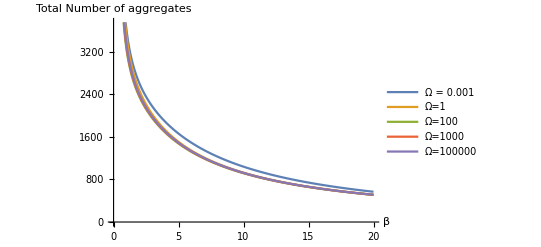

```mathematica
ListLinePlot[{(ⅇ^-J05+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J05×l)×∑_(n=1)^l ⅇ^(-1 x Cos[(n π)/(2 l)]))/(ⅇ^-J05+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J05×l)×∑_(n=1)^l ⅇ^(-1 x Cos[(n π)/(2 l)]))×10000,(ⅇ^-J1+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-1.5 x Cos[(n π)/(2 l)]))/(ⅇ^-J1+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-1.5 x Cos[(n π)/(2 l)]))×10000,(ⅇ^-J105+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-2 x Cos[(n π)/(2 l)]))/(ⅇ^-J105+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-2 x Cos[(n π)/(2 l)]))×10000,(ⅇ^-J2+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-2.5 x Cos[(n π)/(2 l)]))/(ⅇ^-J2+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-2.5 x Cos[(n π)/(2 l)]))×10000,
(ⅇ^-J205+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-3 x Cos[(n π)/(2 l)]))/(ⅇ^-J205+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-3 x Cos[(n π)/(2 l)]))×10000},DataRange->{0,20},PlotLegends->{"Ω = 0.001","Ω=1","Ω=100","Ω=1000","Ω=100000"},AxesLabel->{"β","Total Number of aggregates"}]
```

General::munfl: Exp[-717.887] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-731.692] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-745.498] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

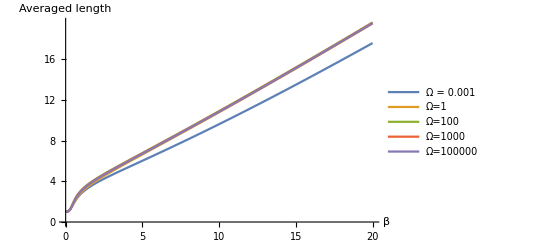

```mathematica
ListLinePlot[{(ⅇ^-J05+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J05×l)×∑_(n=1)^l ⅇ^(-1 x Cos[(n π)/(2 l)]))/(ⅇ^-J05+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J05×l)×∑_(n=1)^l ⅇ^(-1 x Cos[(n π)/(2 l)])),(ⅇ^-J1+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-1.5 x Cos[(n π)/(2 l)]))/(ⅇ^-J1+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J1×l)×∑_(n=1)^l ⅇ^(-1.5 x Cos[(n π)/(2 l)])),(ⅇ^-J105+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-2 x Cos[(n π)/(2 l)]))/(ⅇ^-J105+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J105×l)×∑_(n=1)^l ⅇ^(-2 x Cos[(n π)/(2 l)])),(ⅇ^-J2+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-2.5 x Cos[(n π)/(2 l)]))/(ⅇ^-J2+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J2×l)×∑_(n=1)^l ⅇ^(-2.5 x Cos[(n π)/(2 l)])),
(ⅇ^-J205+gamma×∑_(l=2)^10000 l^4×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-3 x Cos[(n π)/(2 l)]))/(ⅇ^-J205+gamma×∑_(l=2)^10000 l^3×(l-1)^2/(l!)×ⅇ^(-J205×l)×∑_(n=1)^l ⅇ^(-3 x Cos[(n π)/(2 l)]))},DataRange->{0,20},PlotLegends->{"Ω = 0.001","Ω=1","Ω=100","Ω=1000","Ω=100000"},AxesLabel->{"β","Averaged length"}]
```